# THE NUMBER e AS A LIMIT, LOGARITHMIC AND EXPONENTIAL FUNCTIONS Lab #1

Elliott Cable
Due Date: June 16, 2016
Instructor: D. Maslanka

## Objectives

We’ll examine several approaches to defining the irrational exponential e, hopefully finishing with an intuitive understanding of the definition of the number. I’m told several approaches to defining it will be used and compared.

## Problems

1.  In this problem, you will approximate the number  ⅇ  numerically.
     ( a )  Define the function:  f ( x ) = (1+1/x)^x  and the constant function:  g ( x ) =  ⅇ  	  
     	  using Mathematica.

```mathematica
p[x_]:=(1+1/x)^x
```

```mathematica
q[x_]:=Exp[1]
```

( b )   Sketch a graph of  the functions  f  and  g  defined in part  (a)  over the interval
              0  <  x  <  50  and explain, in words, the relationship between these two graphs.
              Hint: Try using the option AspectRatio→1/2 in your Plot instruction.

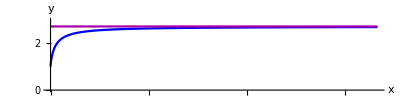

```mathematica
Plot[{p[x],q[x]},{x,0,50},PlotRange->{0,3},PlotStyle->{{Blue,Thickness[0.004]},{Darker[Magenta],Thickness[0.004]}},AspectRatio->1/4,AxesLabel->{x,y}]
```

( c )   Execute the following sequence of instructions within a single cell in order to find 
             the smallest integer  P  which satisfies the inequality:
                                              ⅇ - f ( P ) <  1/100 .

```mathematica
P=1;(* a counter *)
While[Exp[1]-p[P]>=1/100,P=P+1];
P "= P"
```

135 = P

( d )   Find the least integers  Q  and  R  such that:
		    ⅇ - f ( Q ) <  1/1000 = 10^-3
		    ⅇ - f ( R ) <  1/10000= 10^-4
	   by using  While instruction as in part ( c ).

```mathematica
P=1;(* a counter *)
While[Exp[1]-p[P]>=1/1000,P=P+1];
P  "= P"
```

1359 = P

```mathematica
P=1;(* a counter *)
While[Exp[1]-p[P]>=1/10000,P=P+1];
P  "= P"
```

13591 = P

( e )   The values:  f ( P ),  f ( Q ) and  f ( R )  are successively better approximations
               to the number  ⅇ . Use  Mathematica to find decimal representations for these 
               values.
                Note that in Mathematica the instruction: N[f[P]] yields a decimal
                representation of the number  f[P] .

```mathematica
{p[135] // N, p[1359] // N, p[13591] // N}
```

{2.70828,2.71728,2.71818}

2.  When studying Taylor Series in Chapter 11, it will be shown that the sum:

                            1 + 1/(1!) + 1/(2!)  + 1/(3!)  +  . . .  + 1/(n!)      (*)
                         
       converges to the number ⅇ  as  n → ∞.
      
       Recall that k factorial, k ! ,  is defined by:
       
                        k !  =  1 × 2  ×  3  ×  . . . × k   for any positive integer  k  
              and     0 !  =  1 .
              
     The above sum  (*)  may be described in  Mathematica, as the function, Z( n ), where:

```mathematica
Z[n_]:=Sum[1/k!,{k,0,n}]
```

To view the formula for  Z(n) , in sigma notation, execute the following instruction:

```mathematica
TraditionalForm[HoldForm[Sum[1/k!,{k,0,n}]]]
```

∑_(k=0)^n 1/(k!)

( a )   Use a  While loop to find the least integer  n  such that
              Z( n ) differs from  ⅇ  by less than 1/1000.

```mathematica
P=1;(* a counter *)
While[Exp[1]-Z[P]>=1/1000,P=P+1];
P  "= P"
```

6 = P

( b )   Use the approach specified in part  ( a )  to find the least integer  n  such that
              Z( n )  differs from  ⅇ  by less than  1/10000.

```mathematica
P=1;(* a counter *)
While[Exp[1]-Z[P]>=1/10000,P=P+1];
P  "= P"
```

7 = P

( c )  Based on your findings in problems 1 and 2, which of the two sequences:

                       { (1+1/n)^n }_(n-1)^(+∞)         or        {1+1/(1!) + 1/(2!)  + 1/(3!)+   . . .  +1/(n!)}_(n=1)^(+∞)
            
             appears to converge more quickly to the number  ⅇ ?

```mathematica
{Z[6] // N, Z[7] // N,Z[8] // N}
```

{2.71806,2.71825,2.71828}

The former.

3.  ( a )  Use the fact that :

ln n  =∫_1^n 1/t ⅆt

and a pair of associated right and left hand Riemann sums to explain, in words,  why
               the following inequality is valid for any integer n ⩾ 2:   
                
                1/2 + 1/3  + 1/4  +  . . .  + 1/n  <   ln n   <  1 + 1/2 + 1/3    +  . . .  +  1/(n-1)  .                     
              Hint: Use the figure below for reference in this problem. You need not apply any
                       Mathematica instructions in your answer.

-Graphics-

For a given n, …

( b )   Substitute 1,000,000 for  n  in the inequality in part (a) and then apply the  
	       NSum instruction appropriately to obtain upper and lower approximate bounds 
	       on the value of  ln ( 1 000 000) .

```mathematica
{NSum[1/t,{t,2,1000000}],Log[1000000]//N,1+NSum[1/t,{t,2,(1000000-1)}]}
```

{13.3927,13.8155,14.3927}

4.  Apply the Disc Method and Mathematica to obtain and evaluate an integral expression 
        for the volume of the solid generated by rotating the region bounded by: 
                             y  =  ⅇ^( -x^2) ,    y  =  0 ,  x = 0  and  x  =  1  
        about the  y -axis. 
        (Refer to section 5.2 of the Stewart Text for reference, or click on the link:
         notes2  for help with this topic.)
                   
        In our case,

Volume  = ∫_0^1 π[r(y)]^2 ⅆy

where  r ( y_o ) denotes the radius of the cross-section of the solid in the plane
            which is both perpendicular to the y-axis and is y_o units above the x-axis.)
       -Graphics3D-

```mathematica
f[x_]:=E^(-x^2)
```

```mathematica
g[y_]:=±√Log[1/y]
```

```mathematica
∫_0^1 π (±√Log[1/y])^2 ⅆy
```

```mathematica
∫_0^1 π Log[1/y]ⅆy
```

π

## Analysis & Conclusions

I have some slight intuitive understanding of both the (1/x+1)^xand ∑_(k=0)^n 1/k! definitions for e; but it’s not set in concrete: I’m still a little confused by the content of this lab. As for №s. 3 & 4, I’m much more lost: for №. 3 in particular, I have no idea what sort of answer is being sought; I see nothing of meaning in the presented graph …
As for Mathematica issues: I struggled for a few moments with the fact that Mathematica wouldn’t evaluate
Integrate[ Pi * (±Sqrt[Log[1/y]])^2, {x, 0, 1} ] as I expected; but after manually reducing the (±Sqrt[…])^2, I was able to produce a result I was more happy with.